```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
ResourceFunction["PlotGrid"]
```

/Users/james/Documents/Mahmoud uCC RBC Paper 2022

## BEADS

```mathematica
beaddata=Import["yeast & microbeads new device.xlsx"];
beadsheets=Import["yeast & microbeads new device.xlsx","Sheets"]
```

{microbeads,4um,5um,6um,8um,yeast cell& 10%DMSO 0.6ul }

```mathematica
bead4um=Rest@Most@Transpose@Take[Transpose[Drop[beaddata[[2]],3]],{1,5}];
Map[Mean,Transpose@bead4um];
Map[StandardDeviation,Transpose@bead4um];
bead5um=Rest@Transpose@Take[Transpose[Drop[beaddata[[3]],1]],{1,5}];
Map[Mean,Transpose@bead5um];
Map[StandardDeviation,Transpose@bead5um];
bead6um=Rest@Transpose@Take[Transpose[beaddata[[4]]],{1,5}];
Map[Mean,Transpose@bead6um];
Map[StandardDeviation,Transpose@bead6um];
bead8um=Rest@Transpose@Take[Transpose[beaddata[[5]]],{1,5}];
Map[Mean,Transpose@bead8um];
Map[StandardDeviation,Transpose@bead8um];
```

```mathematica
meanStDev[means_,stdevs_,diam_,stepsize_]:=Table[{diam-(3*stepsize)+i stepsize,Around[means⟦i⟧,stdevs⟦i⟧]},{i,Length[means]}]
```

```mathematica
stepsize=0.1;
beadToPlot={
meanStDev[Map[Mean,Transpose@bead4um],Map[StandardDeviation,Transpose@bead4um],4,stepsize],
meanStDev[Map[Mean,Transpose@bead5um],Map[StandardDeviation,Transpose@bead5um],5,stepsize],
meanStDev[Map[Mean,Transpose@bead6um],Map[StandardDeviation,Transpose@bead6um],6,stepsize],
meanStDev[Map[Mean,Transpose@bead8um],Map[StandardDeviation,Transpose@bead8um],8,stepsize]}
```

{{{3.8,0.4800.011},{3.9,0.4880.012},{4.,0.4890.009},{4.1,0.4770.008},{4.2,0.4800.013}},{{4.8,0.5860.009},{4.9,0.5810.007},{5.,0.5800.010},{5.1,0.5800.010},{5.2,0.5780.008}},{{5.8,0.6860.013},{5.9,0.6850.010},{6.,0.6920.010},{6.1,0.6880.011},{6.2,0.6850.010}},{{7.8,0.9880.014},{7.9,0.9920.014},{8.,0.9830.015},{8.1,0.9830.015},{8.2,1.0020.014}}}

```mathematica
normstd[data_]:=StandardDeviation[data/Mean[data]]
meanBeadDeviation=Mean@Map[normstd,Join[Transpose@bead4um,Transpose@bead5um,Transpose@bead6um,Transpose@bead8um]]
STDBeadDeviation=StandardDeviation[Map[normstd,Join[Transpose@bead4um,Transpose@bead5um,Transpose@bead6um,Transpose@bead8um]]]
```

0.0167359

0.0037996

```mathematica
beadToRegress={{4,Mean@Map[Mean,Transpose@bead4um]},{5,Mean@Map[Mean,Transpose@bead5um]},{6,Mean@Map[Mean,Transpose@bead6um]},{8,Mean@Map[Mean,Transpose@bead8um]}};
beadRegress=LinearModelFit[beadToRegress,x,x];beadRegress["RSquared"]
```

0.98815

```mathematica
beaddiamplot=ListPlot[beadToPlot,PlotRange->{.4,1.05},
AspectRatio->1,
PlotStyle->PointSize[Large],
PlotMarkers->"OpenMarkers",
Frame->True,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"Diameter (μm)","Voltage (V)"},
LabelStyle->Directive[Black,Bold,18],
Prolog->{Thick,Gray,Line[{{3.8,beadRegress[3.8]},{8.1,beadRegress[8.1]}}]}];
textXPos=5.45;
traceTicks={{1,1},{2,2},{3,3},{4,6},{5,10}};
beadtraceplot=ListLinePlot[
Join[bead4um,bead5um,bead6um,bead8um],
PlotRange->{{.4,5.9},{.4,1.05}},
AspectRatio->1,
PlotMarkers->None,
Frame->True,
FrameTicks->{{Automatic,Automatic},{traceTicks,None}},
FrameStyle->Directive[Black,Thick],
FrameLabel->{"Electrode","Voltage (V)"},
LabelStyle->Directive[Black,Bold,18],
Epilog->{
Text[Style["4 μm",16],{textXPos,Mean[Flatten[bead4um]]}],
Text[Style["5 μm",16],{textXPos,Mean[Flatten[bead5um]]}],
Text[Style["6 μm",16],{textXPos,Mean[Flatten[bead6um]]}],
Text[Style["8 μm",16],{textXPos,Mean[Flatten[bead8um]]}]
}];
```

```mathematica
beadPlot=[
{
{
beaddiamplot,
beadtraceplot
}
},ImageSize->600
]
```

-Graphics-

```mathematica
Export["beadPlot.png",beadPlot]
```

beadPlot.png

## Experiment 1: Equil RBC Volume

```mathematica
exp1data=Import["e3-RBC-1m.xlsx"];
exp1sheets=Import["e3-RBC-1m.xlsx","Sheets"]
```

{1pbs,1.5pbs,3pbs,5pbs}

```mathematica
exp1PBS1=Drop[exp1data[[1]],7];
exp1PBS1times=Last@exp1PBS1;
exp1PBS1data=Transpose[Rest[Transpose[Drop[exp1PBS1,-10]]]];
exp1PBS15=Drop[exp1data[[2]],7];
exp1PBS15times=Last@exp1PBS15;
exp1PBS15data=Transpose[Rest[Transpose[Drop[exp1PBS15,-7]]]];
exp1PBS3=Drop[exp1data[[3]],7];
exp1PBS3times=Last@exp1PBS3;
exp1PBS3data=Transpose[Rest[Transpose[Drop[exp1PBS3,-11]]]];
exp1PBS5=Drop[exp1data[[4]],7];
exp1PBS5times=Last@exp1PBS5;
exp1PBS5data=Transpose[Rest[Transpose[Drop[exp1PBS5,-7]]]];
```

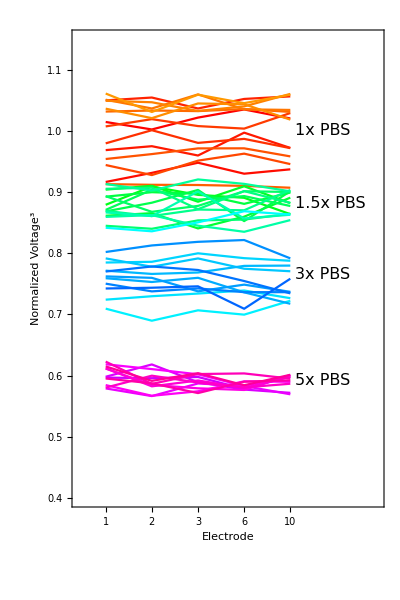

```mathematica
pow=1;
traceTicks={{1,1},{2,2},{3,3},{4,6},{5,10}};
exp1yrange={0.4,1.15};
exp1pbs1color=Table[{i,Hue[i]},{i,0,.1,.1/(Length[exp1PBS1data]-1)}];
exp1pbs15color=Table[{i,Hue[i]},{i,.35,.45,.1/(Length[exp1PBS15data]-1)}];
exp1pbs3color=Table[{i,Hue[i]},{i,.5,.6,.1/(Length[exp1PBS3data]-1)}];
exp1pbs5color=Table[{i,Hue[i]},{i,.8,.9,.1/(Length[exp1PBS5data]-1)}];
exp1colors=Join[exp1pbs1color,exp1pbs15color,exp1pbs3color,exp1pbs5color][[All,2]];
exp1diamticks=Table[{i,Round[i*Mean[Flatten[exp1PBS1data]^pow],.1]},{i,0,1.2,.2}];
textXPos=5.1;
exp1traceplot=ListLinePlot[
Join[
exp1PBS1data^pow/Mean[Flatten[exp1PBS1data]^pow],
exp1PBS15data^pow/Mean[Flatten[exp1PBS1data]^pow],
exp1PBS3data^pow/Mean[Flatten[exp1PBS1data]^pow],
exp1PBS5data^pow/Mean[Flatten[exp1PBS1data]^pow]],
PlotRange->{{.4,6.9},exp1yrange},
PlotStyle->exp1colors,
AspectRatio->1.5,
PlotMarkers->None,
Frame->True,
FrameTicks->{{Automatic,exp1diamticks},{traceTicks,None}},
FrameStyle->Directive[Black,Thick],
FrameLabel->{{"Normalized Voltage^3","Voltage (V)"},{"Electrode",None}},
LabelStyle->Directive[Black,Bold,18],
Epilog->{
Text[Style["1x PBS",16],{textXPos,(Mean[Flatten[exp1PBS1data]]^pow)/(Mean[Flatten[exp1PBS1data]^pow])},{-1,0}],
Text[Style["1.5x PBS",16],{textXPos,Mean[Flatten[exp1PBS15data]]^pow/Mean[Flatten[exp1PBS1data]^pow]},{-1,0}],
Text[Style["3x PBS",16],{textXPos,Mean[Flatten[exp1PBS3data]]^pow/Mean[Flatten[exp1PBS1data]^pow]},{-1,0}],
Text[Style["5x PBS",16],{textXPos,Mean[Flatten[exp1PBS5data]]^pow/Mean[Flatten[exp1PBS1data]^pow]},{-1,0}]
}]
```

```mathematica
meanBeadDeviation=Mean@Map[normstd,Join[Transpose@exp1PBS1data,Transpose@exp1PBS15data,Transpose@exp1PBS3data,Transpose@exp1PBS5data]]
STDBeadDeviation=StandardDeviation[Map[normstd,Join[Transpose@exp1PBS1data,Transpose@exp1PBS15data,Transpose@exp1PBS3data,Transpose@exp1PBS5data]]]
```

0.0370062

0.015057

```mathematica
exp1DataMaker[xpbs_,dataset_]:={1/xpbs,Around[Mean[Flatten[dataset]^pow]/Mean[Flatten[exp1PBS1data]^pow],StandardDeviation[Flatten[dataset]^pow]/Mean[Flatten[exp1PBS1data]^pow]]}
exp1DataMakerR[xpbs_,dataset_]:={1/xpbs,Mean[Flatten[dataset]^pow]/Mean[Flatten[exp1PBS1data]^pow]}
exp1ToPlot=
{exp1DataMaker[1,exp1PBS1data],exp1DataMaker[1.5,exp1PBS15data],exp1DataMaker[3,exp1PBS3data],exp1DataMaker[5,exp1PBS5data]};
exp1ToRegress=
{exp1DataMakerR[1,exp1PBS1data],exp1DataMakerR[1.5,exp1PBS15data],exp1DataMakerR[3,exp1PBS3data],exp1DataMakerR[5,exp1PBS5data]};
exp1Regress=LinearModelFit[exp1ToRegress,x,x];exp1Regress["RSquared"]
exp1Regress["RSquared"]
```

0.924527

0.924527

```mathematica
exp1Regress["BestFitParameters"]
exp1Regress["RSquared"]
```

{0.552259,0.467179}

```mathematica
Total[{0.5522593100180031,0.46717890352577357}]
```

1.01944

```mathematica
Total@Map[Length,{exp1PBS1data,exp1PBS15data,exp1PBS3data,exp1PBS5data}]
```

50

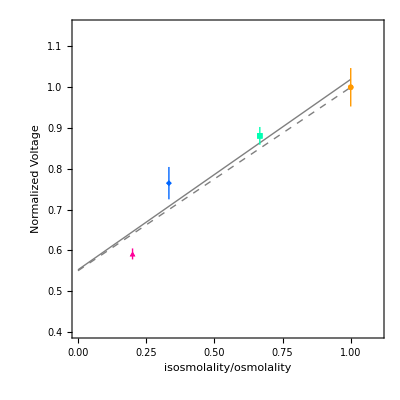

```mathematica
exp1VolPlot=ListPlot[
Partition[exp1ToPlot,1],
PlotRange->{{0,1.1},exp1yrange},
PlotStyle->Map[Last,{exp1pbs1color,exp1pbs15color,exp1pbs3color,exp1pbs5color}][[All,2]],
AspectRatio->1,
PlotMarkers->{Automatic,Scaled[.035]},
Frame->True,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"isosmolality/osmolality","Normalized Voltage"},
LabelStyle->Directive[Black,Bold,18],
Prolog->{
{Thick,Gray,Line[{{0,exp1Regress[0]},{1,exp1Regress[1]}}]},
{Thick,Gray,Dashed,Line[{{0,.55},{1,1}}]}
}]
```

```mathematica
Exp1Plot=[
{
{
exp1VolPlot,
exp1traceplot
}
},ImageSize->650
]
```

-Graphics-

```mathematica
Export["Exp1Plot.png",Exp1Plot]
```

Exp1Plot.png

## Experiment 2: iso->hyper

### preliminaries

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[exp1PBS1data].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[exp1PBS15data].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[exp1PBS3data].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

{result,10pbs-repeated,10pbs,5pbs-repeated,5pbs,3pbs,2pbs-repeated,2pbs,1.5pbs,1pbs-ignore}

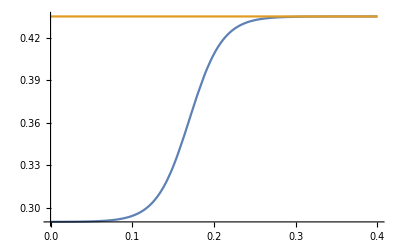

```mathematica
equilVoltage={Mean[Flatten[exp1PBS1data]]^pow,Mean[Flatten[exp1PBS15data]]^pow,Mean[Flatten[exp1PBS3data]]^pow,Mean[Flatten[exp1PBS5data]]^pow}; (*from Above *)
exp2data=Import["e1-boyle van hoff-RBC-after defense.xlsx"];
exp2datasheets=Import["e1-boyle van hoff-RBC-after defense.xlsx","Sheets"]

(*Test Params!*)
temp=273.15+22;
 ciso = .290; 
vbfrac = .55; (*rat Vb, from above *)
viso=67.5;  (*rat RBC Volume --see Lee et al https://doi.org/10.1155/2019/6027236*)
wiso = viso*(1 - vbfrac);
vb=viso*vbfrac;
area=115;(*rat RBC surface area --see Lee et al https://doi.org/10.1155/2019/6027236*)
gasConst=0.083;

cEXTfunc[xPBS_,b_,t_]:=((xPBS-1)*LogisticSigmoid[(t-.17)/b]+1)*ciso

plotter[times_,data_,isovolt_,equilvolt_]:=ListPlot[Table[{times[[i]],data[[i]]},{i,Length[times]}],
Frame->True,
PlotRange->{{0,1},{equilvolt-0.05,isovolt+.05}},
PlotMarkers->{Automatic,Scaled[.07]},
Epilog->
{Dashed,Gray,Line[{{0,equilvolt},{1,equilvolt}}],
Dashed,Gray,Line[{{0,isovolt},{1,isovolt}}]
}]
Clear[sumOfSquares]
sumOfSquares[Lpguess_,b_,xPBS_,data_]:=Module[{sol,pred},
sol=NDSolve[
{w'[t]==-Lpguess*area*gasConst*temp (cEXTfunc[xPBS,b,t]-wiso ciso/w[t]),
w[0]==wiso},w,{t,0,1}];
pred=Map[(w[#]+vb)*data[[-1,-1]]/(w[1]+vb)/.sol&,data[[All,1]]];
Return[First@Total[(pred-data[[All,2]])^2]]]


fitPlotter[Lptest_,dataset_,cext_,equilvolt_,isovolt_,b_,yRange_]:=Module[{sol},
sol=NDSolve[
{w'[t]==-Lptest*area*gasConst*temp (cEXTfunc[cext,b,t]-wiso ciso/w[t]),
w[0]==wiso},w,{t,0,1}];
Show[
Plot[
(w[t]+vb)*dataset[[-1,-1]]/(w[1]+vb)/.sol,{t,0,.9},
PlotRange->yRange,
Frame->True,
PlotStyle->Black,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"time (s)","Voltage"},
LabelStyle->Directive[Black,Bold,18],
Epilog->
Text[
Style[
Row[{"L",Subscript["","p"]," = ",ToString[Lptest]}],18],{.74,.72}]],
ListPlot[dataset,PlotStyle->Black,PlotMarkers->{"OpenMarkers",Scaled[.06]}]]];


Plot[{cEXTfunc[1.5,.02,t],1.5*ciso},{t,0,.4},PlotRange->{1,1.5}*ciso]
```

```mathematica
Solve[ Pw A/W0 == Lp A R T,Lp]
```

{{Lp→Pw/(R T W0)}}

```mathematica
(*From Lahmann, Benson, Higgins 2018; for Pw A/W0 *)
aw=1020; (* s^-1 *)
bw = 2.83; (* kg/osm *)
isosm=.290; (* osm *)
lBHPerm[extmOSM_]:=(aw/(bw (extmOSM+isosm)/2 + 1))/(gasConst*temp*wiso);
```

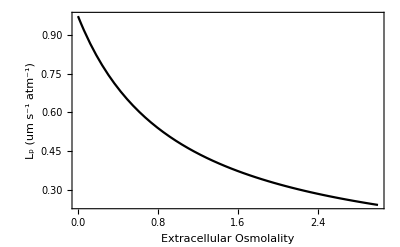

```mathematica
Plot[lBHPerm[x],{x,0,3},
Frame->True,
PlotStyle->Black,
FrameStyle->Directive[Black,Thick],
FrameLabel->{"Extracellular Osmolality","L_p (um s^-1 atm^-1)"},
LabelStyle->Directive[Black,Bold,18]]
```

```mathematica
lBHPerm[(1.5)*ciso]
```

0.676629

### iso->1.5x PBS

```mathematica
xPBS=1.5;
cext = xPBS*ciso;
```

```mathematica
exp2PBS15data=Transpose[Drop[Transpose[Drop[Drop[exp2data[[-2]],5],-8]],1]];
exp2PBS15times=Most@exp2data[[-2,-3]] ;
```

```mathematica
(*Can use to visualize all data at once *)
[Partition[Table[
plotter[exp2PBS15times,exp2PBS15data[[i]],equilVoltage[[1]],equilVoltage[[2]]],{i,Length[exp2PBS15data]}],3],ImageSize->600];
```

ListPlot::prng: Value of option PlotRange -> {{0,1},{-0.05+Mean[Flatten[exp1PBS15data]]^pow,0.05+Mean[Flatten[exp1PBS1data]]^pow}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

```mathematica
pbs15data[i_]:=Table[{exp2PBS15times[[j]],exp2PBS15data[[i,j]]},{j,5}]
```

```mathematica
newlist={};oldlist=RandomReal[{1,2},{Length[exp2PBS15data],3}];
Do[
x2=.001*jjj;
Do[
tab=ParallelTable[{x1,x2,sumOfSquares[x1,x2,xPBS,pbs15data[iii]]},{x1,.1,.9,.01}];
best=First@SortBy[tab,Last];
AppendTo[newlist,best];
rsq[iii,jjj]=1-sumOfSquares[best[[1]],best[[2]],xPBS,pbs15data[iii]]/Total[Part[(pbs15data[iii]-Last@Mean[pbs15data[iii]])^2,All,2]];
,{iii,Length[exp2PBS15data]}];
(*Print["NEW SS: = ",Last[Total[newlist]], "OLD SS: =",Last[Total[oldlist]]];*)
If[(Last@Total[newlist])<(Last@Total[oldlist]),oldlist=newlist; Print[jjj]];
newlist={};
,{jjj,50}]
bestfitlist15=oldlist;
```

1

8

9

10

11

12

13

14

15

16

17

18

19

20

```mathematica
Mean@Table[rsq[iii,20],{iii,Length[bestfitlist15]}]
StandardDeviation@Table[rsq[iii,20],{iii,Length[bestfitlist15]}]
```

0.981196

0.0275312

```mathematica
bestfitlist15//Length
```

19

```mathematica
blank=Plot[1,{x,0,.9},PlotStyle->White,Frame->False,Axes->False]
```

-Graphics-

-Graphics-

```mathematica
Mean[bestfitlist15]
StandardDeviation[bestfitlist15]
```

{0.352632,0.02,0.0000719276}

{0.0540414,0.,0.000111433}

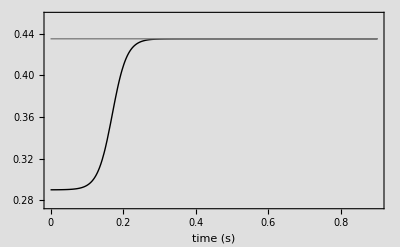

{{0.1923,0.657537},{0.2508,0.607327},{0.3093,0.58608},{0.4848,0.584887},{0.7188,0.585993}}

```mathematica
cextplot=Plot[{cEXTfunc[xPBS,bestfitlist15[[1,2]],t],xPBS*ciso},{t,0,.9},
PlotRange->{0.95,1.05xPBS}*ciso,
Frame->True,
FrameStyle->Directive[Black,Thick],
PlotStyle->{{Thick,Black},{Thick,Gray}},
FrameTicks->{{None,All},{All,None}},
FrameLabel->{{None,"Osm"},{"time (s)",""}},
LabelStyle->Directive[Black,Bold,18],Background->Lighter[Gray, 0.75]]
```

```mathematica
lpfitplot15=[Partition[Append[Table[
fitPlotter[bestfitlist15[[i,1]],pbs15data[i],xPBS,0,0,bestfitlist15[[i,2]],{.55,.75}],{i,Length[bestfitlist15]}],cextplot],4],ImageSize->900]
```

-Graphics-

```mathematica
cEXTfunc[xPBS,bestfitlist15[[1,2]],.19]/(xPBS*ciso)
```

0.910353

```mathematica
Export["cextplot15dynamic.pdf",cextplot]
Export["lpfitplot15dynamic.pdf",lpfitplot15]
Export["lpfitplot15dynamic.png",lpfitplot15]
```

cextplot15dynamic.pdf

lpfitplot15dynamic.pdf

lpfitplot15dynamic.png